```mathematica
Data ={
{0.0, 146.744},
{0.5, 131.289},
{1.0,118.209},
{1.5,111.822},
{2.0,107.272},
{2.5,103.634},
{3.0,92.9625},
{3.5,90.1147},
{4.0,88.1935},
{4.5,83.1547},
{5.0,83.263},
{5.5,76.3783},
{6.0,74.3924},
{6.5, 77.9381},
{7.0, 83.2276},
{7.5,75.5535},
{8.0, 74.0773},
{8.5, 73.4603}};
```

```mathematica
rel=NonlinearModelFit[Data,a*Exp[-x/t]+75,{a,t},x]
rel["ParameterTable"]
rel["AdjustedRSquared"]
```

FittedModel[75+71.6059 ⅇ^(-0.448135 x)]

| Estimate | Standard Error | t-Statistic | P-Value
a | 71.6059 | 2.36473 | 30.2808 | 1.48118×10^-15
t | 2.23147 | 0.116986 | 19.0746 | 1.98394×10^-12

0.998987

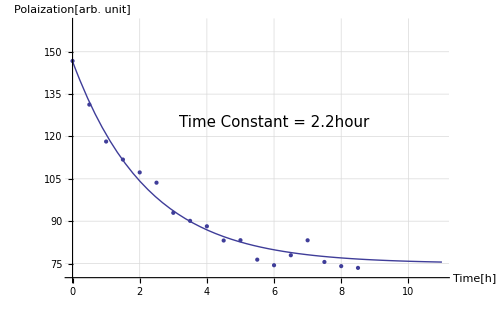

```mathematica
Show[Plot[Normal[rel],{x,0,11}, PlotRange->{70,160},GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted], ImageSize->500, AxesLabel->{"Time[h]","Polaization[arb. unit]"}, Epilog->Text[Style["Time Constant = 2.2hour",15], {6,125}]],
ListPlot[Data]]
```

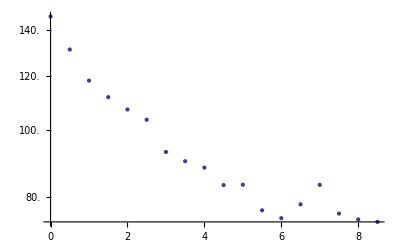

```mathematica
ListLogPlot[Data]
```